## Hamilton equations for a basic system

```mathematica
ClearAll["Global`*"]
```

q -> the coordinate 
qd = dq/dt

```mathematica
(*test function of the Hamiltonian*)
ham[n_,q_,qd_]:=4 qd^2*Sin[q]-Exp[q]+(n+1/2)*π*Sqrt[qd]; 
dhamq[n_,q_,qd_]:=N[D[ham[n,q,qd],q]];
dhamqd[n_,q_,qd_]:=N[D[ham[n,q,qd],qd]];
```

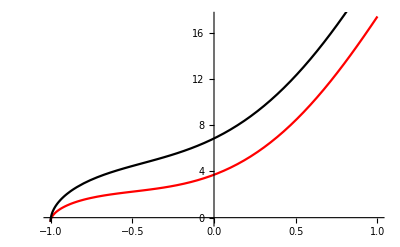

```mathematica
Show[Plot[ham[1,x,x+1],{x,-1,1},PlotStyle->Red],Plot[ham[2,x,x+1],{x,-1,1},PlotStyle->Black]]
```

General::ivar: -0.999959 is not a valid variable.

General::ivar: -0.959143 is not a valid variable.

General::ivar: -0.918326 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

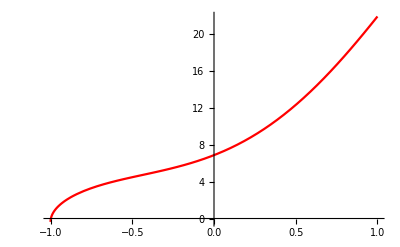

```mathematica
Show[Plot[ham[2,q,q+1],{q,-1,1},PlotStyle->Red],Plot[dhamq[2,x,x+1],{x,-1,1},PlotStyle->Black]]
```

```mathematica
Plot[dhamq[2,x,x+1],{x,-1,1},PlotStyle->Black]
```

General::ivar: -0.999959 is not a valid variable.

General::ivar: -0.959143 is not a valid variable.

General::ivar: -0.918326 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[N[D[Sqrt[x],x]],{x,0.1,1}]
```

General::ivar: 0.100018 is not a valid variable.

General::ivar: 0.118386 is not a valid variable.

General::ivar: 0.136753 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-